## Fig. 1

```mathematica
SetDirectory[NotebookDirectory[]];
mei=1/1836.15267389;
f[x_,α_]=mei/x^2+1/(x-α)^2;
mei2=1/100.;
f2[x_,α_]=mei2/x^2+1/(x-α)^2;
```

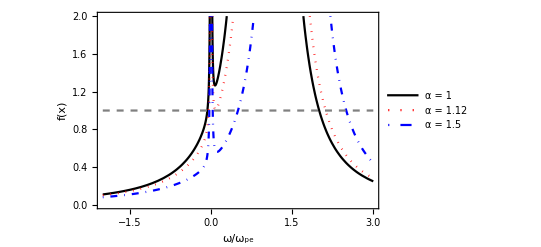

```mathematica
Plot[{f[x,{1,1.12,1.5}]//Evaluate,1},{x,-2,3},PlotRange->{0,2},Frame->True,FrameLabel->{ω/Subscript[ω,Style[pe,Italic]],"f(x)"},PlotStyle->{Black,{Red,Dotted},{Blue,DotDashed},{Dashed,Gray}},PlotLegends->Placed[LineLegend[Table[Style[i,15,FontFamily->"Latin Modern Roman"],{i,{"α = 1","α = 1.12","α = 1.5"}}],LegendFunction->(Framed[#1, FrameMargins->0] & ),LegendMarkerSize->{{20,10},{20,10}}],{0.2,.75}],FrameStyle->Directive[Black,18],BaseStyle->{FontFamily->"Latin Modern Roman"}]
(*Export["two_stream_disp.pdf",%];*)
```

## Necessary math

```mathematica
root=Solve[D[f[x,α],x]==0,x][[3]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{x→0.0754985 α}

```mathematica
alpha=Solve[(f[x,α]/.root)==1,α][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{α→1.12496}

```mathematica
FindRoot[{Re[f[xr+I xi,1]]==1,Im[f[xr+I xi,1]]==1},{{xr,0.1},{xi,0.1}}]
```

{xr→0.224163,xi→0.321837}

```mathematica
root2=Solve[D[f2[x,α],x]==0,x][[3]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{x→0.177255 α}

```mathematica
alpha2=Solve[(f2[x,α]/.root2)==1,α][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{α→1.33999}

```mathematica
α/3/.alpha2
```

0.446664

```mathematica
ans=FindMaximum[xi/.FindRoot[{Re[f2[xr+I xi,α]]==1,Im[f2[xr+I xi,α]]==0},{{xr,0.00002},{xi,0.0001}}],{α,1.1}]//Quiet
```

{0.13647,{α→1.04139}}

```mathematica
α/3/.ans[[2]]
```

0.34713

```mathematica
{(Re[f[xr+I xi,1.]]//ComplexExpand)==1,(Im[f[xr+I xi,α]]//ComplexExpand)==0}//FullSimplify
```

{1./((xi^2+(-1.+xr)^2)^2)-(2. xr)/((xi^2+(-1.+xr)^2)^2)+xi^2 (-1/((xi^2+(-1.+xr)^2)^2)-0.000544617/((xi^2+xr^2)^2))+xr^2 (1/((xi^2+(-1.+xr)^2)^2)+0.000544617/((xi^2+xr^2)^2))==1,(2 xi (-xr+α))/((xi^2+(xr-α)^2)^2)==(0.00108923 xi xr)/((1. xi^2+1. xr^2)^2)}

```mathematica
mei3=100.;
f3[x_,α_]=mei3/x^2+1/(x-α)^2;
root3=Solve[D[f3[x,α],x]==0,x][[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{x→0.822745 α}

```mathematica
alpha3=Solve[(f3[x,α]/.root3)==1,α][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{α→13.3999}

```mathematica
α/10/.alpha3
```

1.33999

```mathematica
ans2=FindMaximum[xi/.FindRoot[{Re[f3[xr+I xi,α]]==1,Im[f3[xr+I xi,α]]==0},{{xr,.4},{xi,.05}}],{α,10}]//Quiet
```

{1.3647,{α→10.4139}}

```mathematica
α/10/.ans2[[2]]
```

1.04139

## Fig. 2

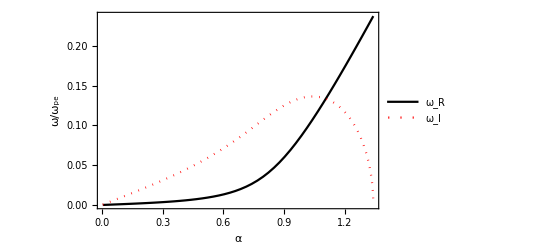

Plot[{xr/.FindRoot[{Re[f2[xr+ⅈ xi,α]]==1,Im[f2[xr+ⅈ xi,α]]==0},{{xr,0.00002},{xi,0.0001}}],xi/.FindRoot[{Re[f2[xr+ⅈ xi,α]]==1,Im[f2[xr+ⅈ xi,α]]==0},{{xr,0.00002},{xi,0.0001}}]},{α,0.005,α0},PlotRange→All,Frame→True,FrameLabel→{α,ω/ω_pe},PlotStyle→{Black,{Red,Dotted}},PlotLegends→Placed[LineLegend[Table[i,{i,{ω_R,ω_I}}],LegendFunction→(#1&),LegendMarkerSize→{{20,10},{20,10}}],{0.15,0.78}],FrameStyle→Directive[Black,18],BaseStyle→{FontFamily→Latin Modern Roman}]

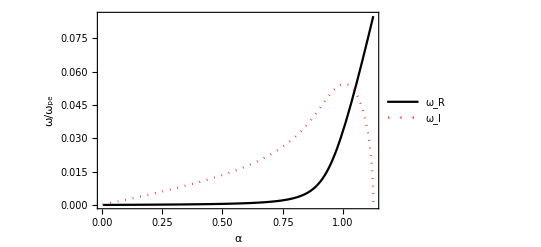

```mathematica
α0=α/.alpha;
Plot[(#/.FindRoot[{Re[f2[xr+I xi,α]]==1,Im[f2[xr+I xi,α]]==0},{{xr,0.00002},{xi,0.0001}}]&/@{xr,xi})//Evaluate,{α,0.005,α0},PlotRange->All,Frame->True,FrameLabel->{α,ω/Subscript[ω,Style[pe,Italic]]},PlotStyle->{Black,{Red,Dotted}},PlotLegends->Placed[LineLegend[Table[Style[i,15,FontFamily->"Latin Modern Roman"],{i,{"ω_R","ω_I"}}],LegendFunction->(Framed[#1, FrameMargins->0] & ),LegendMarkerSize->{{20,10},{20,10}}],{0.15,.78}],FrameStyle->Directive[Black,18],BaseStyle->{FontFamily->"Latin Modern Roman"}]//Quiet
(*Export["omega_roots.pdf",%];*)
```

## Weak cold beam inst

```mathematica
mei=2000;
f[x_,α_]=mei/x^2+1/(x-α)^2;
```

```mathematica
Manipulate[Plot[f[x,α],{x,-100,100},PlotRange->{0,2}],{α,40,70}]
```

```mathematica
rootwcb=Solve[D[f[x,α],x]==0,x][[1]]
```

{x→-(10 (-200 α-2^(1/3) α+10 2^(2/3) α))/2001}

```mathematica
alphawcb=(Solve[(f[x,α]/.rootwcb)==1,α]//N)[[2]]
```

{α→50.15}

## Extra math

```mathematica
FindRoot[Re[f[xr+I xi,1.1]-1],{xr,0.01}]
```

FindRoot::nlnum: The function value {-1.+Re[1/(-1.09+(0.+1. ⅈ) xi)^2+0.000544617/(0.01+Times[«2»])^2]} is not a list of numbers with dimensions {1} at {xr} = {0.01}.

FindRoot[Re[f[xr+ⅈ xi,1.1]-1],{xr,0.01}]

```mathematica
ComplexExpand[Re[f[xr+I xi,1.1]-1]]//FullSimplify
```

-1+1.21/((xi^2+(-1.1+xr)^2)^2)-(2.2 xr)/((xi^2+(-1.1+xr)^2)^2)+xi^2 (-1/((xi^2+(-1.1+xr)^2)^2)-0.000544617/((xi^2+xr^2)^2))+xr^2 (1/((xi^2+(-1.1+xr)^2)^2)+0.000544617/((xi^2+xr^2)^2))

```mathematica
f[xr+I xi,1.1]-1//Expand
```

-1+1/(-1.1+ⅈ xi+xr)^2+0.000544617/(ⅈ xi+xr)^2

```mathematica
1/(-1.1+I xi+xr)^2*1/(-1.1-I xi+xr)^2//FullSimplify
```

1/((1.21+xi^2+(-2.2+xr) xr)^2)

```mathematica
Solve[{FullSimplify[ComplexExpand[Re[f[xr+I xi,α]]]]==1,FullSimplify[ComplexExpand[Im[f[xr+I xi,α]]]]==0},{xr,xi}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{xr→0.5 α-0.5 √(α^2+2.76351×10^-10 (1)+1+1/1+9.2117×10^-11 (1)^(1/3))-0.5 √(2. α^2+3.68468×10^-10 (3.62056×10^9-3.61859×10^9 α^2)-(9.2117×10^-11 (-3.62056×10^9+1)^2)/((-4.74598×10^28+4+1)^(1/3))-9.2117×10^-11 (-4.74598×10^28+1.40908×10^29 α^2-1.42224×10^29 α^4+4.73823×10^28 α^6+5.27917×10^13 √1)^(1/3)-(0.25 (-0.00871387 α+8. α^3-2.21081×10^-9 α (-3.62056×10^9+3.61859×10^9 α^2)))/(√(α^2+2.76351×10^-10 (3.62056×10^9-3.61859×10^9 α^2)+9.2117×10^-11 (-3.62056×10^9+3.61859×10^9 α^2)+(9.2117×10^-11 (-3.62056×10^9+1)^2)/((-4.74598×10^28+4+1)^(1/3))+9.2117×10^-11 (-4.74598×10^28+4+5.27917×10^13 √(4.74598×10^28 α^2-1.41605×10^29 α^4+1.42224×10^29 α^6-4.73823×10^28 α^8))^(1/3)))),xi→0.},14,1}
 |  |  |  |

## Two-Stream

```mathematica
ans=Solve[1==1/(x-α)^2+1/(x+α)^2,x]//FullSimplify
```

{{x→-√(1+α^2-√(1+4 α^2))},{x→√(1+α^2-√(1+4 α^2))},{x→-√(1+α^2+√(1+4 α^2))},{x→√(1+α^2+√(1+4 α^2))}}

```mathematica
ansα=Solve[1+α^2-√(1+4 α^2)==0,α]
```

{{α→0},{α→-√2},{α→√2}}

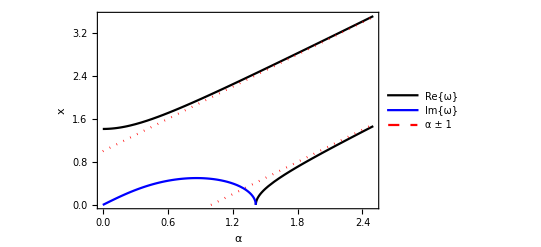

```mathematica
Show[Plot[{x/.ans,α+1,α-1},{α,0,2.5},PlotStyle->{Black,{Red,Dotted},{Red,Dotted}},PlotRange->{0,Automatic},Frame->True,FrameLabel->{α,x},FrameStyle->Directive[Black,18],BaseStyle->{FontFamily->"Latin Modern Roman"},PlotLegends->Placed[LineLegend[{Directive[Black],Directive[Blue],Directive[Red,Dashed]},Table[Style[i,15,FontFamily->"Latin Modern Roman"],{i,{"Re{ω}","Im{ω}","α ± 1"}}],LegendFunction->(Framed[#1, FrameMargins->0] & ),LegendMarkerSize->{{20,10},{20,10}}],{0.16,.76}]],Plot[Im[x]/.ans[[2]],{α,0,α/.ansα[[3]]},PlotStyle->Blue]]
Export["two_real.pdf",%];
```

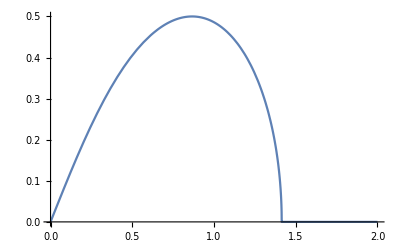

```mathematica
Plot[Im[x]/.ans[[2]],{α,0,2},PlotRange->All]
```

```mathematica
D[1+α^2-√(1+4 α^2),α]//FullSimplify
```

α (2-4/(√(1+4 α^2)))

```mathematica
Solve[4 α^2+1==4,α]
```

{{α→-(√3)/2},{α→(√3)/2}}

```mathematica
√(3/4.)
```

0.866025

```mathematica
v0=10.;
cells=(2π v0)/(√3/2)
```

72.552

```mathematica
2.*Log[1*^16]
```

73.6827

## Buneman

```mathematica
Solve[1==(1/10.)/x^2+1/(x-0.5)^2,x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.646511},{x→0.0621055-0.146781 ⅈ},{x→0.0621055+0.146781 ⅈ},{x→1.5223}}

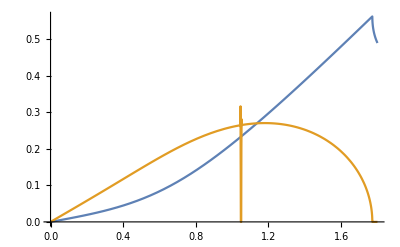

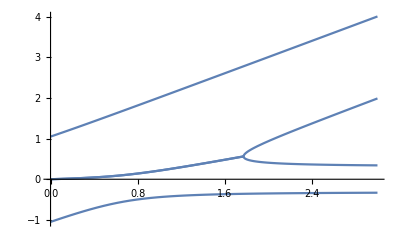

```mathematica
ans=Solve[1==mrat/x^2+1/(x-α)^2,x];
Plot[{Re[x/.ans[[2]]/.mrat->1/10],Im[x/.ans[[2]]/.mrat->1/10]},{α,0,1.8}]
```

```mathematica
Simplify[ans[[2]],Assumptions->{mrat>0,α>0}]
```

{x→1/6 (3 α-√3 √(2+2 mrat+α^2+(1+mrat-α^2)^2/(-1-mrat^3+3 α^2-3 α^4+α^6+3 mrat^2 (-1+α^2)-3 mrat (1+16 α^2+α^4)+6 √3 α √(mrat (mrat^3-3 mrat^2 (-1+α^2)-(-1+α^2)^3+3 mrat (1+7 α^2+α^4))))^(1/3)+(-1-mrat^3+3 α^2-3 α^4+α^6+3 mrat^2 (-1+α^2)-3 mrat (1+16 α^2+α^4)+6 √3 α √(mrat (mrat^3-3 mrat^2 (-1+α^2)-(-1+α^2)^3+3 mrat (1+7 α^2+α^4))))^(1/3))+3 √(1+mrat+α^2+1/3 (1+mrat-α^2)-(1+mrat-α^2)^2/(3 (-1-mrat^3+3 α^2-3 α^4+α^6+3 mrat^2 (-1+α^2)-3 mrat (1+16 α^2+α^4)+6 √3 α √(mrat (mrat^3-3 mrat^2 (-1+α^2)-(-1+α^2)^3+3 mrat (1+7 α^2+α^4))))^(1/3))-1/3 (-1-mrat^3+3 α^2-3 α^4+α^6+3 mrat^2 (-1+α^2)-3 mrat (1+16 α^2+α^4)+6 √3 α √(mrat (mrat^3-3 mrat^2 (-1+α^2)-(-1+α^2)^3+3 mrat (1+7 α^2+α^4))))^(1/3)+(2 √3 (-1+mrat) α)/(√(2+2 mrat+α^2+(1+mrat-α^2)^2/(-1-mrat^3+3 α^2-3 α^4+α^6+3 mrat^2 (-1+α^2)-3 mrat (1+16 α^2+α^4)+6 √3 α √(mrat (mrat^3-3 mrat^2 (-1+α^2)-(-1+α^2)^3+3 mrat (1+7 α^2+α^4))))^(1/3)+(-1-mrat^3+3 α^2-3 α^4+α^6+3 mrat^2 (-1+α^2)-3 mrat (1+16 α^2+α^4)+6 √3 α √(mrat (mrat^3-3 mrat^2 (-1+α^2)-(-1+α^2)^3+3 mrat (1+7 α^2+α^4))))^(1/3)))))}

## BoT

```mathematica
mei=100;
f[x_,α_]=mei/x^2+1/(x-α)^2;
```

```mathematica
Solve[
```

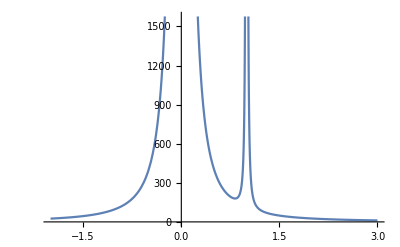

```mathematica
Plot[{f[x,1]},{x,-2,3}]
```

```mathematica
Plot[{f[x,{1,1.12,1.5}]//Evaluate,1},{x,-2,3},PlotRange->{0,2},Frame->True,FrameLabel->{ω/Subscript[ω,Style[pe,Italic]],"f(x)"},PlotStyle->{Black,{Red,Dotted},{Blue,DotDashed},{Dashed,Gray}},PlotLegends->Placed[LineLegend[Table[Style[i,15,FontFamily->"Latin Modern Roman"],{i,{"α = 1","α = 1.12","α = 1.5"}}],LegendFunction->(Framed[#1, FrameMargins->0] & ),LegendMarkerSize->{{20,10},{20,10}}],{0.2,.75}],FrameStyle->Directive[Black,18],BaseStyle->{FontFamily->"Latin Modern Roman"}]
(*Export["two_stream_disp.pdf",%];*)
```

-Graphics-

## Necessary math

```mathematica
root=Solve[D[f[x,α],x]==0,x][[1]]//N
```

{x→0.822745 α}

```mathematica
alpha=Solve[(f[x,α]/.root)==1,α][[2]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{α→13.3999}

```mathematica
Solve[c/(a α)^2+1/(a α-α)^2==1,α]//FullSimplify
```

{{α→-(√(a^2+(-1+a)^2 c))/(√((-1+a)^2 a^2))},{α→(√(a^2+(-1+a)^2 c))/(√((-1+a)^2 a^2))}}

```mathematica
FindRoot[{Re[f[xr+I xi,1]]==1,Im[f[xr+I xi,1]]==1},{{xr,7},{xi,3}}]
```

{xr→7.81933,xi→-3.23312}

```mathematica
ComplexExpand[c/x^2+1/(x-α)^2-1,{x}]
```

-1-(c Im[x]^2)/((Im[x]^2+Re[x]^2)^2)+(c Re[x]^2)/((Im[x]^2+Re[x]^2)^2)+α^2/((Im[x]^2+(-α+Re[x])^2)^2)-Im[x]^2/((Im[x]^2+(-α+Re[x])^2)^2)-(2 α Re[x])/((Im[x]^2+(-α+Re[x])^2)^2)+Re[x]^2/((Im[x]^2+(-α+Re[x])^2)^2)+ⅈ (-(2 c Im[x] Re[x])/((Im[x]^2+Re[x]^2)^2)+(2 α Im[x])/((Im[x]^2+(-α+Re[x])^2)^2)-(2 Im[x] Re[x])/((Im[x]^2+(-α+Re[x])^2)^2))

```mathematica
FullSimplify[-1-(c Im[x]^2)/((Im[x]^2+Re[x]^2)^2)+(c Re[x]^2)/((Im[x]^2+Re[x]^2)^2)+α^2/((Im[x]^2+(-α+Re[x])^2)^2)-Im[x]^2/((Im[x]^2+(-α+Re[x])^2)^2)-(2 α Re[x])/((Im[x]^2+(-α+Re[x])^2)^2)+Re[x]^2/((Im[x]^2+(-α+Re[x])^2)^2),Assumptions->{α∈Reals,c∈Reals}]
FullSimplify[-(2 c Im[x] Re[x])/((Im[x]^2+Re[x]^2)^2)+(2 α Im[x])/((Im[x]^2+(-α+Re[x])^2)^2)-(2 Im[x] Re[x])/((Im[x]^2+(-α+Re[x])^2)^2),Assumptions->{α∈Reals,c∈Reals}]
```

-1+c/Abs[x]^2-(2 c Im[x]^2)/Abs[x]^4+(Abs[x]^2-2 Im[x]^2+α (α-2 Re[x]))/((Abs[x]^2+α (α-2 Re[x]))^2)

2 Im[x] ((α-Re[x])/((Abs[x]^2+α (α-2 Re[x]))^2)-(c Re[x])/Abs[x]^4)

## Fig. 2

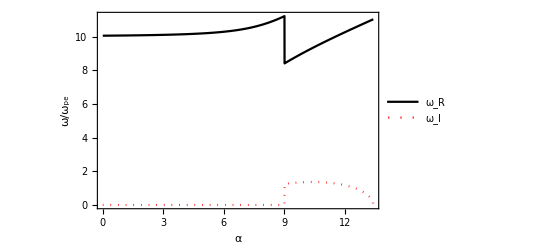

```mathematica
α0=α/.alpha;
Plot[(#/.FindRoot[{Re[f[xr+I xi,α]]==1,Im[f[xr+I xi,α]]==0},{{xr,6},{xi,3}}]&/@{xr,xi})//Evaluate,{α,0.005,α0},PlotRange->All,Frame->True,FrameLabel->{α,ω/Subscript[ω,Style[pe,Italic]]},PlotStyle->{Black,{Red,Dotted}},PlotLegends->Placed[LineLegend[Table[Style[i,15,FontFamily->"Latin Modern Roman"],{i,{"ω_R","ω_I"}}],LegendFunction->(Framed[#1, FrameMargins->0] & ),LegendMarkerSize->{{20,10},{20,10}}],{0.15,.78}],FrameStyle->Directive[Black,18],BaseStyle->{FontFamily->"Latin Modern Roman"}]//Quiet
(*Export["omega_roots.pdf",%];*)
```